## Input Data

```mathematica
PupRSB = {6.747444800213845,13.09111025542305,10.207605995058572,11.360888114720908,9.630908918709373,10.784310455582057,9.05419670323294,7.900738518043493,6.170838451237953,3.863735241632027,0.9803707460056053,9.05419670323294,5.593943932180552};
PupBSB = {3.863735241632027,8.477487117135322,17.128034157872715,34.429104274725184,59.22709096997295,76.52831393816284,88.6391130314905,90.94580329676725,71.33795024215074,48.2698953132471,24.625146040523326,10.784310455582057,3.863735241632027};

ωdet = -0.3
ωstep = 0.05
ωdat = Table[ωdet  + i ωstep,{i,0,12}];

freqapproxRSB = 10512.850;
freqapproxBSB = 11372.649;

dataRSB  = Transpose[{ωdat+ freqapproxRSB, PupRSB }];
dataBSB  = Transpose[{ωdat+ freqapproxBSB, PupBSB }];
```

-0.3

0.05

## Functions

```mathematica
Ω0approx = 0.333;
fitFunc[A_, Ω0_,ω_,ω0_] := A Ω0^2/(Ω0^2+(ω-ω0)^2) Sin[(√(Ω0^2+(ω-ω0)^2)π)/(2 Ω0)]^2;
fitRSB=FindFit[dataRSB,{fitFunc[A0,Ω0,ω,ω0] ,{ ω0>freqapproxRSB + ωdet , ω0 <freqapproxRSB + ωdet + 13ωstep}},{{A0,0},{Ω0,Ω0approx},{ω0,freqapproxRSB}},ω]
fitBSB =FindFit[dataBSB,{fitFunc[A0,Ω0,ω,ω0] ,{ ω0>freqapproxBSB + ωdet , ω0 <freqapproxBSB + ωdet + 13ωstep}},{{A0,0},{Ω0,Ω0approx},{ω0,freqapproxBSB}},ω]
```

{A0→10.2771,Ω0→0.526509,ω0→10512.6}

{A0→89.7774,Ω0→0.181889,ω0→11372.7}

## Output

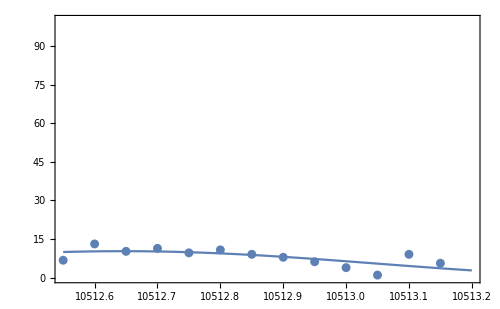

```mathematica
Show[ListPlot[dataRSB],
Plot[fitFunc[A0, Ω0, ω, ω0]/.fitRSB, {ω,freqapproxRSB + ωdet, freqapproxRSB + ωdet + 13ωstep}],
PlotRange-> {{freqapproxRSB + ωdet, freqapproxRSB + ωdet + 13ωstep},{0,100}},
Frame-> True, ImageSize-> 500]
```

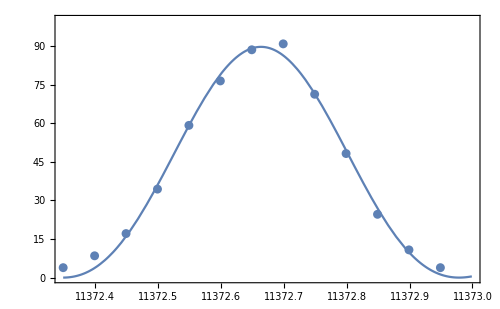

```mathematica
Show[ListPlot[dataBSB],
Plot[fitFunc[A0, Ω0, ω, ω0]/.fitBSB, {ω,freqapproxBSB + ωdet, freqapproxBSB + ωdet + 13ωstep}],
PlotRange-> {{freqapproxBSB + ωdet, freqapproxBSB + ωdet + 13ωstep},{0,100}},
Frame-> True, ImageSize-> 500]
```

## Final nbar

```mathematica
fitRSB = {A0-> Max[PupRSB]}
nbar = (A0/.fitRSB) / (A0/.fitBSB)
```

{A0→13.0911}

0.145817

## Fit to nbar

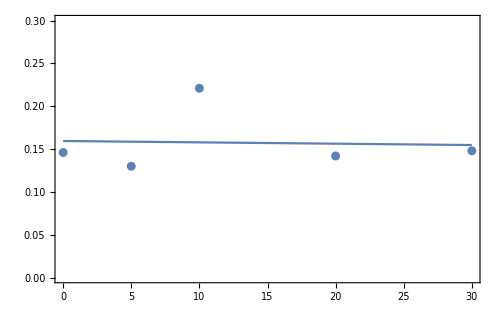

```mathematica
nbarData = {0.146, 0.130, 0.221, 0.142, 0.148};
timeData = {0, 5, 10, 20, 30};
heatingData = Transpose[{timeData, nbarData}];

heatingFit = FindFit[heatingData, x ndot + n0 ,{{ndot, 0.001}, {n0, 0.1}},x];

Show[ListPlot[heatingData],
Plot[(x ndot + n0)/.heatingFit, {x,0,30}],
PlotRange-> {{0, 30},{0,0.3}},
Frame-> True, ImageSize-> 500]
```